```mathematica
用4个频率成分来逼近
```

{1.54293,{t→0.422836}}

{1.54293,{t→2.02034}}

T = 1.5975

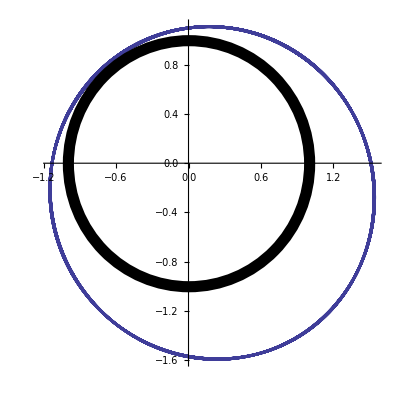

```mathematica
tm=10;coef=4.0 π^2;
xinitial={0,6.5};yinitial={1.1,0.8};
equ={x''[t]==-(coef*x[t])/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-(coef*y[t])/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equ,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
(*...finding period and frequence...*)
peak1=FindMaximum[x[t],{t,0.5}]
peak2=FindMaximum[x[t],{t,2}]
T=(t/.peak2[[2]])-(t/.peak1[[2]]);
Print["T = ",T];ω0=2π/T;
(*...constructing appoximation functions...*)
xcons=0.593999/2+1.32888 Sin[ω0 t-0.26107]+
0.150173 Sin[2ω0 t+0.172142]+
0.02545 Sin[3ω0 t+0.60426];
ycons=-0.726566/2+1.33253 Sin[ω0 t+1.32316]+
0.150448 Sin[2ω0 t+1.75195]+
0.0254853 Sin[3ω0 t+2.18186];
g1=ParametricPlot[{x[t],y[t]},{t,0,tm},
PlotStyle->Thickness[0.005]];
g2=ParametricPlot[{xcons,ycons},{t,0,tm},
PlotStyle->Thickness[0.005]];
Show[{g1,g2},AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13},
Epilog->{Thickness[0.02],Circle[{0,0},1]}]
Clear[x,y]
```